-Graphics-

# Content Authoring

## Notebook Programming Environment & Documentation

```mathematica
Entity["Chemical","AdenosineTriphosphate"]["MoleculePlot"]
```

-Graphics3D-

Paul Abbott
abbott@wolfram.com

-Graphics-

## Getting Started

The Welcome Screen has a link to the Documentation Center

Start with the Notebook Basics guide

Then walk through the Working in Notebooks workflow guide

## Videos and Courses

Courses on Wolfram U

Twitch stream of developer presentations on new functionality in Version 12

Recorded Lectures from the Wolfram Technology Conference

## Free-form Input

Integration with Wolfram|Alpha means that you can use free-form linguistics. The output shows you the syntax required to do the same computation.

-Graphics- (== at beginning of input) — use free-form linguistics to generate WL output

(== == at beginning of input) — generate full Wolfram|Alpha output

-Graphics- (Ctrl+==) — enter free-form linguistics for conversion to inline input

### Getting Help

Compute π to 1000 digits:

pi to 1000 digits

Get the code to plot a function:

plot sin x

Get the code to compute an integral:

int x sin x

Compute the integral of sin(x^2) with x ranging from 0 to ∞:

int sin(x^2) from 0 to inf

Compute the exact value of ∑_(n=1)^∞ 1/n^2

sum 1/n^2

### Harder Questions

Solve the simultaneous equations x^3+y^3==1 and x+y==1/2:

solve x^3 + y^3  = 1 and x + y = 1/2

Solve the ODE y''(x)+y(x)==0:

solve y''+y=0

Produce a contour plot of ⅇ^(-x^2-y^2)sin(x+y) over [-1,1]×[-1,1]

contour plot e^(-x^2 - y^2) sin(x + y) for -1<x<1 and -1<y<1

### Unit Conversion

There are two main unit discovery mechanisms: Ctrl+= and Quantity

The result of this query is a Quantity expression:

3ft

3 ft

UnitConvert takes a list of Quantity expressions and attempts to standardize their units:

3ft in m

Obtain the speed of light in imperial units:

speed of light in mph

Note that this result is exact.

### Atomic Units

Use -Graphics-  to compute ℏ^2/(m_e a_0^2) via the “expected” shortcuts (hbar, m_e, and a_0):

Convert to SI:

```mathematica
UnitConvert[%,"SI"]
```

Express this in eV:

```mathematica
UnitConvert[%,"eV"]
```

Express this in Hartrees:

```mathematica
UnitConvert[%,"Hartrees"]
```

### Chemistry Electronic Laboratory Notebooks

#### Reaction equation

It is easy to construct a diagram of the balanced equation for the reaction of benzylamine with benzoyl chloride:

```mathematica
LinguisticAssistant+LinguisticAssistant==LinguisticAssistant+LinguisticAssistant
```

#### Notable Chemical Compounds

View the Notable Chemical Compounds page and the related Chemical Data information.

Find a property value for an entity:

```mathematica
Entity["Chemical","AdenosineTriphosphate"]["MoleculePlot"]
```

-Graphics3D-

Retrieve a list of all available properties for an entity:

```mathematica
Entity["Chemical","DimethylSulfoxide"]["Properties"]
```

{K_a,adjacency matrix,alternate names,atom positions,autoignition point,Beilstein number,black structure diagram,boiling point,bond counts,bond energies,bond lengths,CAS number,black carbon-hydrogen structure diagram,carbon-hydrogen structure diagram,PubChem CID number,codons,structure diagram,molar heat of combustion,critical pressure,critical temperature,density,dielectric constant,dipole moment,DOT hazard class,DOT numbers,drug interactions,edge rules,edge types,EGEC number,electron affinity,element counts,element mass fraction,element types,entity classes,EU number,flash point,formal charges,formatted name,formula,formula string,molar heat of fusion,Gmelin number,H-bond acceptor count,H-bond donor count,Henry law constant,Hildebrand solubility parameter,Hill formula,Hill formula string,InChI identifier,ion counts,ion equivalents,ions,isoelectric point,isomeric SMILES identifier,isomers,IUPAC name,Lewis dot structure,speed of light,pK_a,lower explosive limit,MDL number,mean free path,melting point,memberships,molar mass,molar volume,molecular mass,molecule plot,name,net ionic charge,NFPA fire rating,NFPA hazards,NFPA health rating,NFPA label,NFPA reactivity rating,non-hydrogen count,non-standard isotope count,non-standard isotope counts,non-standard isotope numbers,NSC number,odor threshold,odor,partition coefficient (XLogP),pH,phase,proton affinity,refractive index,relative molecular mass,resistivity,rotatable bond count,RTECS classes,RTECS number,pK_a of side-chain,SMILES identifier,solubility,space filling molecule plot,standard name,3D molecule skeletal structure,surface tension,tautomer count,molar thermal conductivity,topological polar surface area,upper explosive limit,van der Waals constants,vapor density,molar heat of vaporization,vapor pressure,vertex coordinates,vertex types,dynamic viscosity}

Retrieve a dataset of all available properties for an entity:

```mathematica
Entity["Chemical","DimethylSulfoxide"]["Dataset"]
```

Dataset[<>]

## Typesetting and Interface

### Completion and Templates

Use the Input Assistant to complete functions and provide function templates:

```mathematica
Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
```

Create your own usage message and template:

```mathematica
g[x_,y_]:=(x - 1)(y+ 1)
```

```mathematica
g::usage="g[x,y] gives (x - 1)(y + 1)";
```

```mathematica
?g
```

### Iconize

Use Iconize to simplify function calls:

```mathematica
Plot[Sin[x],{x,0,10},Filling->Axis,Mesh->All]
```

Apply the Iconize command to a Sequence of options:

```mathematica
Iconize[Sequence[Filling->Axis,Mesh->All,PlotRange->1/2],"Options"]
```

Copy and paste these options into another plot:

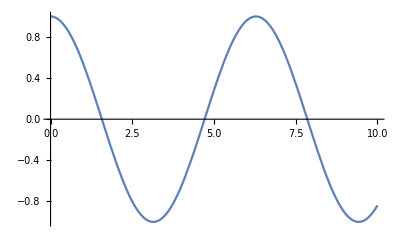

```mathematica
Plot[Cos[x],{x,0,10}]
```

## TraditionalForm versus StandardForm

The default input and output FormatType is StandardForm which provides good readable two-dimensional typeset input and output and is mathematically unambiguous because it uses Mathematica syntax.

TraditionalForm is an enhanced format corresponding to mathematical syntax, as far as this is consistently possible.

One can convert input and output cells to TraditionalForm. Alternatively, one can use the Option Inspector to change the CommonDefaultFormatTypes, which I have done for the following section.

### Advantages

1. Matrices can be entered and are displayed in two-dimensional form without requiring MatrixForm:

```mathematica
({{a, b}, {c, d}}).({{a, b, c}, {d, e, f}})
```

(a^2+b d | a b+b e | a c+b f
a c+d^2 | b c+d e | c^2+d f)

2. Derivatives can be entered in their familiar two-dimensional form:

```mathematica
(ⅆg(u,v))/ⅆx
```

ⅆv/ⅆx g^(0,1)(u,v)+ⅆu/ⅆx g^(1,0)(u,v)

3. Standard notation is available for limits and directional limits:

```mathematica
lim_(x->0^-) (sin(x))/(|x|)
```

-1

4. Mathematical expressions are easier to read:

```mathematica
Assuming[m<1,∫_0^(π/2) 1/(√(1-m sin^2(θ)))ⅆθ]
```

(m/(m-1))/(√(1-m))

Hold your mouse over this output to see what function has been generated.

5. Where it is not ambiguous, special functions are interpreted automatically. For example, here is the derivative of the Bessel function, J_n(z):

```mathematica
(∂Subscript[J, n](z))/(∂z)
```

1/2 (n-1z-n+1z)

6. Special function names and syntax correspond to that found in standard tables:

```mathematica
Hypergeometric2F1[1,1,2,x]
```

7. Complicated functions can be much easier to digest:

```mathematica
MeijerG[{{a},{b,c}},{{d,e},{f,g,h}},z]
```

G_(3,5)^(2,1)(z|a,b,c
d,e,f,g,h)

7. Templates for a wide range of functions is available, for example 6j symbols:

```mathematica
{ {{Subscript[j, 1], Subscript[j, 2], Subscript[j, 3]}, {Subscript[j, 4], Subscript[j, 5], Subscript[j, 6]}} }
```

### Notation Package

The Notation Package allows you to define arbitrary input and output syntaxes for functions of your choosing.

#### Load the Package

Load the Notation package.

```mathematica
<<Notation`
```

#### Define a Tensor Notation

The following declares a notation for Tensor objects. The second rule handles cases with zero indices and multiple indices (due to the way that Subsuperscript is defined, implicitly with one upper and one lower index only).

```mathematica
Notation[Subscript[x_, l_]^u_ ⟺ Tensor[x_][l_][u_]]
```

```mathematica
Notation[Subscript[x_, l___]^u___ ⟺ Tensor[x_][l___][u___]]
```

Notations defined using ⟺ in their definition both parse and format expressions according to the given notation. However, you can restrict the notation to only parsing or only formatting by using ⟹ or ⟸ respectively, instead of ⟺ in your notation statements.

Any tensor input is now interpreted as a Tensor object but displayed as a formatted tensor.

```mathematica
Tensor[R][i][j, k]
```

R_i^(j,k)

One can see the underlying (internal) structure using FullForm.

```mathematica
FullForm[%]
```

Tensor[R][i][j,k]

Any Tensor expression is now formatted in the new notation.

```mathematica
Tensor[x][α][γ,δ]
```

x_α^(γ,δ)

#### Add an Input Alias

A Tensor expression can be input most easily using an input alias.

```mathematica
AddInputAlias["tensor"->■_□^□]
```

Now one can get an input template by typing EsctensorEsc. One then simply needs to “fill in the blanks”, moving between placeholders (fields) using the ⇥ key.

#### Add Rules

One can add rules for the manipulation of Tensor objects.

Index lowering and index raising is achieved via the metric tensor. These rules are associated with Tensor via TagSet (or /: ).

```mathematica
Clear[Tensor]
```

```mathematica
Tensor/:g_^(i_,j_)Subscript[x_, j_,l___]^m___:=Subscript[x, l]^(i,m)
```

```mathematica
Tensor/:Subscript[g, α_,β_]^g_^(β_,γ_):=Subscript[δ, α]^γ
```

#### Test it Out

Two example of index gymnastics:

```mathematica
g_^(i,j) Subscript[A, j]^
```

A_^i

```mathematica
Subscript[g, i,j]^ g_^(j,k)
```

δ_i^k

## Using Packages

The Setting Up Wolfram Language Packages tutorial is a good overview

See also Ian Johnson’s  Wolfram Summer School 2017 presentation

### Why Packages?

To distribute codes

Organizes code in a usable way

More advanced Wolfram Language projects use paclets

### Packages vs Notebooks

#### Notebooks (.nb)

Easy to use

Very general

Powerful graphics

Editable

Difficult to distribute and maintain

#### Wolfram Language Packages (.wl)

Convenient to distribute

Easy to load

Useful for documentation

Includes usage messages and templates

Hierarchical structure

Includes custom editing tools

Abstract implementation from user

### Package Example

Open the package WignerEisenbud.wl assuming that it is located in the same directory as this notebook:

```mathematica
SetDirectory[NotebookDirectory[]];FrontEndExecute[FrontEndToken["Open"]]
```

### Workflows

Use the Package Editor

Wolfram Workbench + Eclipse

Your favorite text editor

### Source Control

GitLink is a package for integrating git functionality into the Wolfram Language

This is not ideal for Notebooks but works very well for packages

Search for Mathematica packages on github

### Testing and Debugging

There is a useful Testing Framework

Workbench tests

See the Tuning and Debugging guide and use RuntimeTools`